## VersionRequired

```mathematica
VersionRequired::vtl = "Mathematica 版本过低. 当前的版本为 ``, 要求的版本为 ``."; 
VersionRequired[v_?NumericQ] := If[TrueQ[$VersionNumber < v], Message[VersionRequired::vtl, $VersionNumber, v]]; 

VersionRequired[10]
VersionRequired[20]
```

VersionRequired::vtl: Mathematica 版本过低. 当前的版本为 13.2, 要求的版本为 20.

## ExpressionCoefficient

```mathematica
SetAttributes[ExpressionCoefficient,Listable];
ExpressionCoefficient[expr_,x_Symbol]:=Module[{coef},
If[FreeQ[expr,x],Return[expr]];
coef=Replace[expr//Simplify,c_?(FreeQ[#1,x]&) _->c];
If[!FreeQ[coef,x],coef=1];
coef
];
ExpressionCoefficient[{0,1,-1,(a+b)/2,2/(a+b),x,-x},x]
```

{0,1,-1,(a+b)/2,2/(a+b),1,-1}

## ExpressionPivot

```mathematica
SetAttributes[ExpressionPivot,Listable];
ExpressionPivot[expr_]:=Module[{counts},
counts=Counts@Cases[expr,_Symbol,All];
If[Length@counts===0,Return[False]];
Keys[TakeLargest[counts,1]][[1]]
];

ExpressionPivot[{1,x,a/(a+b)}]
```

{False,x,a}

## IBP

```mathematica
IBP[u_, v_, x_Symbol] := Module[{result,coef},
result=v D[u, x];
coef=ExpressionCoefficient[result,x];
u v-coef result/coefx//Simplify
];
IBP[f_, x_Symbol] := IBP[f, x, x]; 
IBP[u_, v_, {x_Symbol, a_, b_}] :=Module[{result,coef},
result=v D[u, x];
coef=ExpressionCoefficient[result,x];
Limit[u v,x->b]-Limit[u v,x->a]-coef result/coefxab//Simplify
];
IBP[f_, {x_Symbol, a_, b_}] := IBP[f, x, {x, a, b}]; 

IBP[a x^2+b x+c,Sin[α x],x]
IBP[Sin[α Log[x]],x]
```

(c+x (b+a x)) Sin[x α]-(b+2 a x) Sin[x α]x

x Sin[α Log[x]]-α Cos[α Log[x]]x

## IBS

```mathematica
Options[IBS]:={Assumptions->$Assumptions};
IBS[f_,ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]&&FreeQ[et,x]:=
Module[{assum=OptionValue[Assumptions],u},
VersionRequired[13.1];
Simplify[If[ex===x,f/.x->et,IntegrateChangeVariables[fx,u,u==ex,Assumptions->assum]⟦1⟧/.u->et]
D[et,t]/.C[_]->0,assum]
];
IBS[f_,x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[et,x]:=IBS[f,x->et,x,t,opts];
IBS[f_,ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]:=IBS[f,ex->t,x,t,opts];
IBS[f_,{a_,b_},ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]&&FreeQ[et,x]:=
Module[{assum=OptionValue[Assumptions],u,temp},
VersionRequired[13.1];
temp=If[ex===x,fxab/.x->u,IntegrateChangeVariables[fxab,u,u==ex,Assumptions->assum]];
Simplify[If[et===t,temp/.u->t,IntegrateChangeVariables[temp,t,u==et,Assumptions->assum]],assum]
];
IBS[f_,{a_,b_},x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[et,x]:=IBS[f,{a,b},x->et,x,t,opts];
IBS[f_,{a_,b_},ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]:=IBS[f,{a,b},ex->t,x,t,opts];

IBS[x^2,E^x->E^t,x,t,Assumptions->x>0&&t>0]
IBS[x^2,{0,1},2x->E^t,x,t]
```

t^2

ⅇ^(3 t)/8t-∞Log[2]

## ApartArcTan

```mathematica
Options[ApartArcTan]:={GenerateConstant->False,SimplifyFunction->Simplify};
SetAttributes[ApartArcTan,Listable];
ApartArcTan[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=
Module[{simp,gene,roots,result,zeros,offset},
gene=OptionValue[GenerateConstant];
simp=OptionValue[SimplifyFunction];
roots=x/.Solve[expr==ⅈ,x];
result=Sum[ArcTan[simp[(x-Re[r])/Im[r]]],{r,roots}];
If[!gene,Return[result]];
zeros=x/.Solve[Denominator@Together@expr==0,x];
result+=If[Length[zeros]===0,
ArcTan[expr]-result/.x->0,
zeros=DeleteDuplicates[zeros];
offset=Append[
Table[lim_(x->i^-) ArcTan[expr]-(result/.x->i),{i,zeros}],
lim_(x->Last[zeros]^+) ArcTan[expr]-(result/.x->Last[zeros])
];
Piecewise[
Append[
Prepend[
Table[{offset⟦i+1⟧,zeros⟦i⟧<x<zeros⟦i+1⟧},{i,Length[zeros]-1}]
,{First[offset],x<First[zeros]}]
,{Last[offset],x>Last[zeros]}]
]
];
result//Simplify
];
ApartArcTan[expr_,opts:OptionsPattern[]]:=ApartArcTan[expr,ExpressionPivot[expr],opts];

ApartArcTan[{x^2,t+1/t,u-1/u},GenerateConstant->True]//Column
```

1/2 (π-2 ArcTan[1-√2 x]-2 ArcTan[1+√2 x])
ArcTan[(2 t)/(1-√5)]+ArcTan[(2 t)/(1+√5)]+(Piecewise[{{-π/2, t<0}, {π/2, t>0}, {0, True}}])
-ArcTan[√3-2 u]+ArcTan[√3+2 u]+(Piecewise[{{π/2, u<0}, {-π/2, u>0}, {0, True}}])

## RealFactor

```mathematica
Options[RealFactor]:={SimplifyFunction->(Simplify@ToRadicals@RootReduce@#&)};
SetAttributes[RealFactor,Listable];
RealFactor[poly_?PolynomialQ,x_Symbol,OptionsPattern[]]/;CoefficientList[poly,x]∈Reals:=
Module[{simp,sol},
simp=OptionValue[SimplifyFunction];
If[FreeQ[poly,x],Return[poly]];
sol=Sort[x/.Solve[poly==0,x]];
Do[
If[i>Length@sol,Break[]];
If[sol⟦i⟧∈Reals,
sol[[i]]=x-simp[sol⟦i⟧],
sol[[i]]=x^2-simp[sol⟦i⟧+sol⟦i+1⟧] x+simp[sol⟦i⟧ sol⟦i+1⟧];
sol=Delete[sol,i+1];
]
,{i,Infinity}];
Coefficient[poly,x,Exponent[poly,x]] Times@@sol
];
RealFactor[poly_,opts:OptionsPattern[]]:=RealFactor[poly,ExpressionPivot[poly],opts];

RealFactor[x^4-x^2+x+1]
(*BUG*)
RealFactor[(x^2+1)^2]
```

(1+x) (1/3 (-1+(1/2 (25-3 √69))^(1/3)+(1/2 (25+3 √69))^(1/3))+x) (((9-√69)^(1/3)+(9+√69)^(1/3))/(2^(1/3) 3^(2/3))-1/3 (2+(1/2 (25-3 √69))^(1/3)+(1/2 (25+3 √69))^(1/3)) x+x^2)

(-1-2 ⅈ x+x^2) (-1+2 ⅈ x+x^2)

## RealApart

```mathematica
Options[RealApart]:=Options[RealFactor];
SetAttributes[RealApart,Listable];
RealApart[poly_,x_Symbol,opts:OptionsPattern[]]/;RationalExpressionQ[poly,x]:=(Numerator@poly)/RealFactor[Denominator@poly,opts]//Apart;
RealApart[poly_,opts:OptionsPattern[]]:=RealApart[poly,ExpressionPivot[poly],opts];

RealApart[{1/(x^2-5),1/(x^4+x^2-1)}]
```

{-1/(2 √5 (√5-x))-1/(2 √5 (√5+x)),-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))-2 x)-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))+2 x)-2/(√5 (1+√5+2 x^2))}

## CorrectionTest

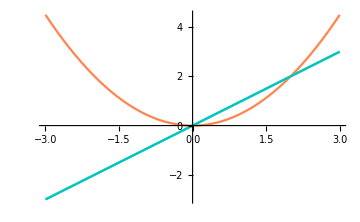
定义域 | 间断点
x∈ℝ | False
x∈ℝ | False
图像 | 
-Graphics- |

```mathematica
Options[CorrectionTest]:={Skip->{},TimeConstraint->∞,VerifyDiscontinuities->{},WorkingPrecision->$MinPrecision};
CorrectionTest::overtime="`` 计算超时";
CorrectionTest[org_,res_,{x_,xmin_,xmax_},OptionsPattern[]]:=
Module[{
table={{Style["定义域",Bold], Style["间断点",Bold]}, {Style[True,Bold,RGBColor["#4081ff"]], Style[False,Bold,RGBColor["#4081ff"]]}, {Style[True,Bold,RGBColor["#eb7100"]], Style[False,Bold,RGBColor["#eb7100"]]}, {Style["图像",Bold], }, {Null, }},
skip=OptionValue[Skip],
cons=OptionValue[TimeConstraint],
veri=OptionValue[VerifyDiscontinuities],
prec=OptionValue[WorkingPrecision],
dom=True
},
VersionRequired[12.2];
If[!ListQ[skip],skip={skip}];
If[!ListQ[veri],veri={veri}];
If[!AssociationQ[cons],cons=Association["定义域"->cons,"间断点"->cons,"图像"->cons]];
If[!MemberQ[skip,"定义域"],
TimeConstrained[
table⟦2,1⟧=Item[Style[dom=Reduce[FunctionDomain[org,x],x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,1⟧=Item[Style[Reduce[FunctionDomain[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["定义域"],Message[CorrectionTest::overtime,"定义域"];
];
];
If[!MemberQ[skip,"间断点"],
TimeConstrained[
table⟦2,2⟧=Item[Style[Reduce[FunctionDiscontinuities[org,x]&&dom,x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,2⟧=Item[Style[Reduce[FunctionDiscontinuities[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["间断点"],Message[CorrectionTest::overtime,"间断点"];
];
];
If[!MemberQ[skip,"图像"],
TimeConstrained[
table⟦5,1⟧=Plot[
{org,res,Evaluate[D[(res/.{Abs[p_]->Piecewise[{{p, p>0}, {-p, p<0}}],Sign[p_]->Piecewise[{{1, p>0}, {-1, p<0}}]}), x]]},{x,xmin,xmax},
PlotStyle->96,ImageSize->Medium,
Epilog->{Black,PointSize[Medium],Point[
Block[{$MinPrecision=prec},N@Table[{i,res/.x->i},{i,veri}]]
]}
],cons["图像"],Message[CorrectionTest::overtime,"图像"];
];
];
Print[Grid[table,Alignment->{Center,Center},Spacings->{1,1},ItemSize->{Scaled[0.5],Automatic},Frame->All]];
];

CorrectionTest[x,x^2/2,{x,-3,3}]
```